```mathematica
Lecture 10: Multivariable Calculus
```

Key multivariable calculus functions include:

```mathematica
{Limit,D,Integrate,NIntegrate,RegionPlot3D,Grad,Hyperplane,FrenetSerretSystem,Curl,Div}
```

## Limits

### Exercise Subsection

Plot the function defined in the next cell using Plot3D for values of x and y between -1 and 1 and then use the graphic to predict the output of the cell containing the Limit functions.

```mathematica
f[x_,y_]:=x y/(x^2+y^2);
```

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->100]
```

-Graphics3D-

```mathematica
{Limit[f[x,y],x->0],
Limit[f[x,y],y->0],
Limit[f[x,y],{x->0,y->x}],
Limit[f[x,y],{x,y}->{0,0}]}
```

{0,0,1/2,Indeterminate}

## Partial derivatives

### Exercise Subsection

Show that the function u[t,x] defined in the next cell satisfies the partial differential equation
D[u[t,x],{t,2}] == k^2 D[u[t,x],{x,2}] together with the initial conditions u[0,x] giving f[x] and D[u[t,x],t] when evaluated at t=0 gives g[x].

```mathematica
Clear[f,g,u,k]
u[t_,x_]:= 1/2 (f[-k t+x]+f[k t+x])+1/(2 k)∫_(-k t+x)^(k t+x) g[s]ⅆs
```

```mathematica
D[u[t,x],{t,2}]==k^2 D[u[t,x],{x,2}]//Simplify
```

True

```mathematica
u[0,x]
```

f[x]

```mathematica
D[u[t,x],t]/.{t->0}
```

g[x]

### Exercise Subsection

Let f[x,y] be the function defined in the following cell

```mathematica
f[x_,y_]:=Cos[x]Cos[y]Exp[-Sqrt[x^2 + y^2]/4]
```

Use Plot3D to visualize this function where x and y can take values between -2π and 2π.  Use ContourPlot to show the level curves on this same interval.  Then take the gradient of this function using Grad and then use VectorPlot on the result, overlaying the VectorPlot on top of the ContourPlot to show that the level curves and the gradient vectors are always perpendicular.

```mathematica
Plot3D[f[x,y],{x,-2π,2π},{y,-2π,2π},PlotRange->{-1,1},PlotPoints->200]
```

-Graphics3D-

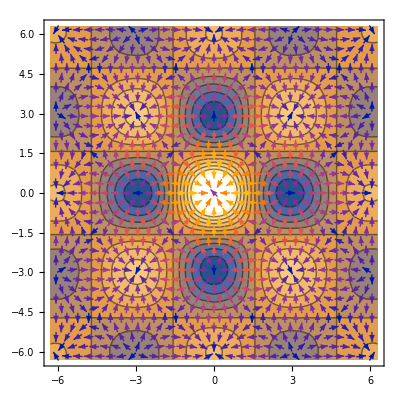

```mathematica
Show[ContourPlot[f[x,y],{x,-2 Pi,2Pi},{y,-2Pi,2Pi}],VectorPlot[Evaluate@Grad[f[x,y],{x,y}],{x,-2 Pi,2Pi},{y,-2Pi,2Pi},VectorPoints->30]]
```

### Exercise Subsection

The critical points of a function f[x, y] are where the gradient vector Grad[f[x, y], {x, y}] is equal to the zero vector.  Use Show to show both the Plot3D to plot the function (y^2+x) Exp[-y^2-x^2] together with Graphics3D to place points on the graph where there are critical points.

```mathematica
f[x_,y_]:=(y^2+x) Exp[-y^2-x^2]
```

```mathematica
points={x,y,f[x,y]}/.Solve[Evaluate@Grad[f[x,y],{x,y}]=={0,0}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{1/2,-1/(√2),1/ⅇ^(3/4)},{1/2,1/(√2),1/ⅇ^(3/4)},{-1/(√2),0,-1/(√(2 ⅇ))},{1/(√2),0,1/(√(2 ⅇ))}}

```mathematica
Show[Plot3D[f[x,y],{x,-1,1},{y,-1,1}],
Graphics3D[{Blue,PointSize[.02],Point@points}]]
```

-Graphics3D-

### Exercise Subsection

The method of Lagrange multipliers can solve a constrained maximization problem of the form (maximize f[x,y]) subject to the constraint that (g[x,y] == 0).  The idea is to find all points that satisfy Grad[f[x,y],{x,y}] = λ Grad[g[x,y],{x,y}] as well as the constraint g[x,y] == 0.  Then test all points that satisfy these equations, one of them is the maximum.

Maximize x Exp[x y] subject to the constraint x^2 + y^2/4 - 1 == 0 using the method of Lagrange multipliers.

```mathematica
f[x_,y_]:=x Exp[x y]
g[x_,y_]:=x^2 + y^2/4 - 1
```

```mathematica
f[First@#,Last@#]&/@Select[{x,y}/.N@Solve[Append[First@#==λ Last@#&/@Transpose@{Grad[f[x,y],{x,y}],Grad[g[x,y],{x,y}]},g[x,y]==0]],Element[#,Reals]&]
```

{-2.09642,2.09642}

## Integration

### Exercise Subsection

a. Use RegionPlot3D to plot the coordinates that satisfy 0<x<y<z<x z+y x+y z<1.  Then find the volume of this region by evaluating an integral of the form 

NIntegrate[f[x,y,z] Boole[0<x<y<z<x z+y x+y z<1], {x, -∞, ∞} , {y, -∞, ∞}, {z, -∞, ∞}]

```mathematica
RegionPlot3D[0<x<y<z<x z+y x+y z<1,{x,0,1},{y,0,1},{z,0,1},PlotPoints->100]
```

-Graphics3D-

```mathematica
NIntegrate[1 Boole[0<x<y<z<x z+y x+y z<1], {x, -∞, ∞} , {y, -∞, ∞}, {z, -∞, ∞}]
```

0.0205207

b . Verify that your answer in part a. makes sense by applying the Monte Carlo method to estimate the volume of this region.  Do this by setting x, y, and z to be different random real numbers between 0 and 1, testing to see if the appropriate inequalities hold, and then repeating this experiment many times over to find a probability that a random {x,y,z} coordinate will lie within the desired region.

```mathematica
test[]:=Module[{x=Random[],y=Random[],z=Random[]},0<x<y<z<x z+y x+y z<1]
```

```mathematica
Count[Table[test[],{i,10^6}],True]/10^6//N
```

0.020578

### Exercise Subsection

The x-coordinate for the center of mass of a region R in R^3 is given the triple integral of x over the region R divided by the volume of the region.  The y and z-coordinates for the center of mass are defined analogously.

Use RegionPlot3D to plot the region in R^3 that satisfies the inequalities 0<z<1, 0<y<z^2, and 0<x<y z.  Use the options PlotPoints->100, PlotStyle->{Opacity[.5]}, Mesh->None to create a nice image.

Then find the center of mass for this region, and place a point at the center of mass into the graphic produced by RegionPlot3D.

```mathematica
RegionPlot3D[0<z<1&&0<y<z^2&&0<x<y z,{x,0,1},{y,0,1},{z,0,1},PlotPoints->100,PlotStyle->{Opacity[.5]},Mesh->None]
```

-Graphics3D-

```mathematica
NIntegrate[x Boole[0<z<1&&0<y<z^2&&0<x<y z], {x, -∞, ∞} , {y, -∞, ∞}, {z, -∞, ∞}]/NIntegrate[1 Boole[0<z<1&&0<y<z^2&&0<x<y z], {x, -∞, ∞} , {y, -∞, ∞}, {z, -∞, ∞}]
```

0.222222

## Tangent planes and vectors

### Exercise Subsection

The graphics primitive Hyperplane[n,p] gives the plane in R^3 that is normal (perpendicular) to n and contains the point p.  If z=f[x,y] is the equation of a surface in R^3, then the gradient vector Grad[z-f[x,y],{x,y,z}] gives a vector perpendicular to the surface.

Show a 3D plot of the surface z=1-x^2-y^2 together with the plane tangent to the surface at the {x,y} coordinate {1/2,0}.

```mathematica
Show[Plot3D[1-x^2-y^2,{x,-1,1},{y,-1,1}],Graphics3D[Hyperplane[{1,0,1},{1/2,0,1-x^2-y^2/.{x->1/2,y->0}}]]]
```

-Graphics3D-

```mathematica
Grad[z-(1-x^2-y^2),{x,y,z}]/.{x->1/2,y->0}
```

{1,0,1}

### Exercise Subsection

Let f[t] be the curve in R^3 described by the parametric equations in the cell below

```mathematica
f[t_]:={Sin[t]+2 Sin[2 t],Cos[t]-2 Cos[2 t],-Sin[3 t]}
```

```mathematica
ParametricPlot3D[f[t],{t,0,2Pi}]
```

-Graphics3D-

where t can range from 0 to 2π.  Each point on a curve in R^3 has a corresponding unit tangent vector T, an unit normal vector N, and a unit binomial vector B.  These three vectors are given by the last component of the output of

frame = FrenetSerretSystem[f[t],t]

```mathematica
frame = Last@FrenetSerretSystem[f[t],t];
```

Use Manipulate to Plot the 3D curve described by f[t] together with three vectors with starting point at f[t] and in the directions of T, N, and B as t ranges from 0 to 2π.  This can be done more easily with commands such as Arrow[{f[t], f[t] + frame[[1]]}] /. {t -> a}.

```mathematica
Manipulate[Show[ParametricPlot3D[f[t],{t,0,2Pi}],
Graphics3D[{Red,Thickness[.01],Arrow[{f[t], f[t] + frame[[1]]}] /. {t -> a},Green,
Arrow[{f[t], f[t] + frame[[2]]}] /. {t -> a},Blue,Arrow[{f[t], f[t] + frame[[3]]}] /. {t -> a}
}]],{a,0,2Pi}]
```

### Exercise Subsection

An arbitrary parametric curve in R^3 can be defined by

```mathematica
Clear[f,x,y,z]
f[t_]:={x[t],y[t],z[t]}
```

Use this arbitrary curve to show that the acceleration of f (this is the second derivative of f) is orthogonal (meaning the dot product is 0) with the unit binomial vector B (the last component of the last component in FrenetSerretSystem[f[t],t]).

### Exercise Subsection

The first component of the first component of FrenetSerretSystem gives the curvature of the parametric curve.  This curvature measures how “curvy” the curve is at a given value of t.  Find the curvature for a circle of radius a in the x,y plane (take the z coordinate to be 0) and for a helix of the form {a Cos[t], a Sin[t], b t}.

## Line integrals and vector fields

### Exercise Subsection

a. Use VectorPlot to plot the 2 dimensional vector field F[x_,y_]:={x-y,x} for values of x and y between -2 and 2.  Consider playing with the options VectorScaling, VectorSizes, and VectorPoints.  Compare this with the command StreamPlot, which also plots the vector field.

```mathematica
F[x_,y_]:={x-y,x}
```

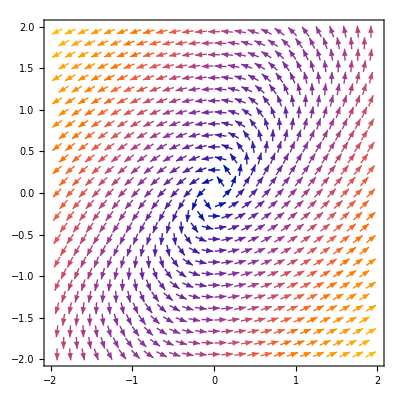

```mathematica
VectorPlot[{x-y,x},{x,-2,2},{y,-2,2},VectorPoints->25]
```

b. The work done by the 3 dimensional vector field F[x,y,z] when traveling along the parametric curve {x[t],y[t],z[t]} for values of t ranging from a to b is equal to ∫_a^b F[x[t],y[t],z[t]].{x'[t],y'[t],z'[t]}ⅆt.  The work done by the 2 dimensional vector field is similar but without the z component.  

Find the work done by the vector field in part a. when traveling along the unit circle once in the counterclockwise direction.

```mathematica
Integrate[F[Cos[t],Sin[t]].{D[Cos[t],t],D[Sin[t],t]},{t,0,2Pi}]
```

2 π

### Exercise Subsection

Use an arbitrary function (such as Clear[f]; f[x,y,z]) and a arbitrary vector field (such as Clear[P,Q,R]; {P[x,y,z],Q[x,y,z],R[x,y,z]}) to show that the curl (see Curl) of the gradient vector is the zero vector and the divergence (see Div) of the curl is equal to 0.